```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Folgendes Integral soll minimiert bzw. maximiert (Vorzeichen des Integrandens wird invertiert) werden:

ℐ=∫_t_1^t_2 F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→min , bzw.  ℐ=∫_t_1^t_2 -F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→max

In dem Funktionenvektor 𝓏_1 sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) vorkommen.
In dem Funktionenvektor 𝓏_2 hingegen sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) nicht vorkommen. 𝓏_2 ist in der Regel ausschließlich im 3. Fall vorhanden!

3. Fall: Ein weiteres Differentialgleichungssystem (𝓏̇)_1=𝒻(t,𝓏_1,𝓏_2) soll erfüllt werden (falls eine oder mehrere Differentialgleichungen höherer Ordnung auftreten, müssen diese zunächst in Differentialgleichungssysteme höheren Grades umgewandelt und zu einem Differentialgleichungssystem zusammengefasst werden).

Für das resultierende Differentialgleichungssystem gilt (λ ist im Gegensatz zum 2. Fall keine Konstante, sondern ein Vektor):

H(t,𝓏_1, (𝓏̇)_1,𝓏_2,λ)=F(t,𝓏_1, (𝓏̇)_1,𝓏_2)+𝒻[t,𝓏_1,𝓏_2]^T·λ
ⅆ/ⅆt (0
λ
𝓏_1)=(∇_𝓏_2 
-∇_𝓏_1
∇_λ ) H(t,𝓏_1, (𝓏̇)_1,𝓏_2,λ)

## Eingabe (F, 𝓏_1, 𝓏_2, 𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃, 𝒻)

```mathematica
ClearAll["Global`*"]
F[t_]=y1[t]^2+y2[t]^2+v2[t]^2;
𝓏1[t_]={y2[t],v2[t]};
𝓏2[t_]={y1[t]};
𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃={y1[0]==1,y1[2]==0,y2[0]==0,y2[2]==1};
𝒻[t_]={v2[t],-v2[t]-y2[t]+y1[t]};
```

## Programm (automatisch)

```mathematica
(*Programm*)
<<VariationalMethods`
λ[t_]={λ1[t],λ2[t]};
H[t_]=F[t]+(𝒻[t]-D[𝓏1[t],t]).λ[t];
𝓏[t_]=Join[𝓏2[t],𝓏1[t],λ[t]];
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽=Table[
FullSimplify[VariationalD[H[t],𝓏[t],t]][[i]]==0,
{i,Length[𝓏[t]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽//TableForm]]
```

2 y1[t]+λ2[t]==0
2 y2[t]-λ2[t]+λ1'[t]==0
2 v2[t]+λ1[t]-λ2[t]+λ2'[t]==0
v2[t]-y2'[t]==0
-v2[t]+y1[t]-y2[t]-v2'[t]==0

## Programm (manuell)

```mathematica
(*Programm*)
λ[t_]={λ1[t],λ2[t]};
H[t_]=F[t]+𝒻[t].λ[t];
𝓏[t_]=Join[𝓏1[t],𝓏2[t],λ[t]];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ1=Table[
FullSimplify[Grad[H[t],𝓏2[t]][[i]]]==0,
{i,Length[𝓏2[t]]}];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ2=Table[
FullSimplify[-Grad[H[t],𝓏1[t]][[i]]]==D[λ[t],t][[i]],
{i,Length[𝓏1[t]]}];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ3=Table[
FullSimplify[Grad[H[t],λ[t]][[i]]]==D[𝓏1[t],t][[i]],
{i,Length[𝓏1[t]]}];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ=Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ1,𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ2,𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ3];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm]]
```

2 y1[t]+λ2[t]==0
-2 y2[t]+λ2[t]==λ1'[t]
-2 v2[t]-λ1[t]+λ2[t]==λ2'[t]
v2[t]==y2'[t]
-v2[t]+y1[t]-y2[t]==v2'[t]

λ_2=-2 y_1
ⅆ/ⅆt(λ_1
-2 y_1
y_2
v_2)=(-2 y_1-2 y_2
-2 y_1-λ_1-2 v_2
v_2
y_1-y_2-v_2)
ⅆ/ⅆt(λ_1
y_1
y_2
v_2)=(-2 y_1-2 y_2
y_1+λ_1/2+v_2
v_2
y_1-y_2-v_2)

```mathematica
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ={
D[λ1[t],t]==-2y1[t]-2y2[t],
D[y1[t],t]==y1[t]+λ1[t]/2+v2[t],
D[y2[t],t]==v2[t],
D[v2[t],t]==y1[t]-y2[t]-v2[t]};

𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm
```

λ1'[t]==-2 y1[t]-2 y2[t]
y1'[t]==v2[t]+y1[t]+λ1[t]/2
y2'[t]==v2[t]
v2'[t]==-v2[t]+y1[t]-y2[t]

## DGL

```mathematica
(*Programm*)
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t_]=Flatten[FullSimplify[N[DSolve[Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ,𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],{y1[t],y2[t],v2[t],λ1[t]},t]]]]
```

{v2[t]→ⅇ^((-0.840896-0.840896 ⅈ) t) ((-0.14243+0.259043 ⅈ)-(0.14243+0.259043 ⅈ) ⅇ^((0.+1.68179 ⅈ) t)+(0.150232+0.0336194 ⅈ) ⅇ^(1.68179 t)+(0.150232-0.0336194 ⅈ) ⅇ^((1.68179+1.68179 ⅈ) t)),y1[t]→ⅇ^((-0.840896-0.840896 ⅈ) t) ((0.125829-0.0777338 ⅈ)+(0.125829+0.0777338 ⅈ) ⅇ^((0.+1.68179 ⅈ) t)+(0.374171+0.0448789 ⅈ) ⅇ^(1.68179 t)+(0.374171-0.0448789 ⅈ) ⅇ^((1.68179+1.68179 ⅈ) t)),y2[t]→ⅇ^((-0.840896-0.840896 ⅈ) t) ((-0.0693385-0.238718 ⅈ)-(0.0693385-0.238718 ⅈ) ⅇ^((0.+1.68179 ⅈ) t)+(0.0693385+0.109319 ⅈ) ⅇ^(1.68179 t)+(0.0693385-0.109319 ⅈ) ⅇ^((1.68179+1.68179 ⅈ) t)),λ1[t]→ⅇ^((-0.840896-0.840896 ⅈ) t) ((-0.309147-0.443505 ⅈ)-(0.309147-0.443505 ⅈ) ⅇ^((0.+1.68179 ⅈ) t)-(0.344052+0.710798 ⅈ) ⅇ^(1.68179 t)-(0.344052-0.710798 ⅈ) ⅇ^((1.68179+1.68179 ⅈ) t))}

```mathematica
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]]]]]
```

{v2[t]→ⅇ^(-0.840896 t) ((-0.284861+0.300465 ⅇ^(1.68179 t)) Cos[0.840896 t]+(0.518087+0.0672388 ⅇ^(1.68179 t)) Sin[0.840896 t]),y1[t]→ⅇ^(-0.840896 t) ((0.251658+0.748342 ⅇ^(1.68179 t)) Cos[0.840896 t]+(-0.155468+0.0897578 ⅇ^(1.68179 t)) Sin[0.840896 t]),y2[t]→ⅇ^(-0.840896 t) ((-0.138677+0.138677 ⅇ^(1.68179 t)) Cos[0.840896 t]+(-0.477435+0.218638 ⅇ^(1.68179 t)) Sin[0.840896 t]),λ1[t]→ⅇ^(-0.840896 t) ((-0.618295-0.688103 ⅇ^(1.68179 t)) Cos[0.840896 t]+(-0.88701-1.4216 ⅇ^(1.68179 t)) Sin[0.840896 t])}

## Plot

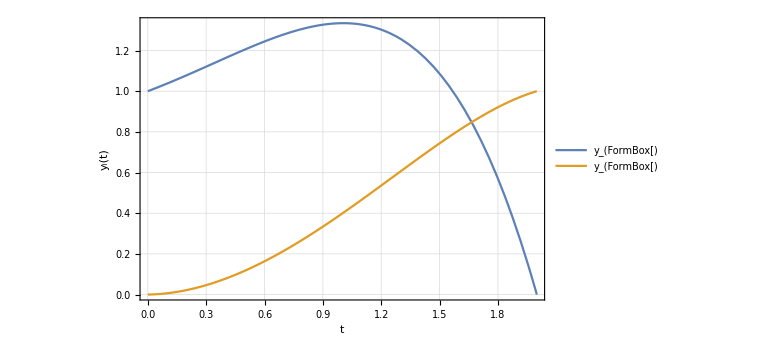

```mathematica
plot=Plot[Evaluate[{y1[t]/.𝓎[t],y2[t]/.𝓎[t]}],{t,0,2},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
ImageSize->Large];
Print[Show[plot]]
```